# Adiabatic Quantum Computing Applied to the 3-SAT Problem

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

Quantum Adiabatic Commputing encodes a problem to be solved in a Hamiltonian (energy operator) in such way that its state of minimum energy ("ground state") represents the solution. Therefore adiabatic evolution of a quantum system to the ground state of the Hamiltonian and subsequent measurement gives the solution to the problem. This document uses Quantum`Computing` Mathematica add-on to implement Adiabatic Quantum Computing applied to the 3-SAT problem.

The concept of Quantum Adiabatic Commputing was created by Edward Farhi, Jeffrey Goldstone, Sam Gutmann, Michael Sipser (2000). "Quantum Computation by Adiabatic Evolution". arΧiv:quant-ph/0001106v1.

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package:

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (June 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## The 3-SAT Problem

A "clause" in the 3-SAT problem is an expression that has the form:
x_1∨x_2∨x_3
where each x is a boolean variable or a negation of a boolean variable. 

This is an example of a clause
q_3∨¬q_6∨¬q_8
where each q_k can be either FALSE or TRUE, and ¬q_k is the negation of q_k.
Clauses will be identified in the following tables with a number such that, when this number is written in binary and 0 is interpreted as FALSE and 1 as TRUE,  it is the only combination of values of q_k that does not satisfy (i.e. makes FALSE) the corresponding clause.

These are the eight possible clauses used in the 3-SAT:

Clause 0 |  |  |  | 
q_a | q_b | q_c | q_a∨q_b∨q_c | 
False | False | False | False | 0
False | False | True | True | 1
False | True | False | True | 2
False | True | True | True | 3
True | False | False | True | 4
True | False | True | True | 5
True | True | False | True | 6
True | True | True | True | 7

Clause 1 |  |  |  | 
q_a | q_b | q_c | q_a∨q_b∨¬q_c | 
False | False | False | True | 0
False | False | True | False | 1
False | True | False | True | 2
False | True | True | True | 3
True | False | False | True | 4
True | False | True | True | 5
True | True | False | True | 6
True | True | True | True | 7

Clause 2 |  |  |  | 
q_a | q_b | q_c | q_a∨¬q_b∨q_c | 
False | False | False | True | 0
False | False | True | True | 1
False | True | False | False | 2
False | True | True | True | 3
True | False | False | True | 4
True | False | True | True | 5
True | True | False | True | 6
True | True | True | True | 7

Clause 3 |  |  |  | 
q_a | q_b | q_c | q_a∨¬q_b∨¬q_c | 
False | False | False | True | 0
False | False | True | True | 1
False | True | False | True | 2
False | True | True | False | 3
True | False | False | True | 4
True | False | True | True | 5
True | True | False | True | 6
True | True | True | True | 7

Clause 4 |  |  |  | 
q_a | q_b | q_c | ¬q_a∨q_b∨q_c | 
False | False | False | True | 0
False | False | True | True | 1
False | True | False | True | 2
False | True | True | True | 3
True | False | False | False | 4
True | False | True | True | 5
True | True | False | True | 6
True | True | True | True | 7

Clause 5 |  |  |  | 
q_a | q_b | q_c | ¬q_a∨q_b∨¬q_c | 
False | False | False | True | 0
False | False | True | True | 1
False | True | False | True | 2
False | True | True | True | 3
True | False | False | True | 4
True | False | True | False | 5
True | True | False | True | 6
True | True | True | True | 7

Clause 6 |  |  |  | 
q_a | q_b | q_c | ¬q_a∨¬q_b∨q_c | 
False | False | False | True | 0
False | False | True | True | 1
False | True | False | True | 2
False | True | True | True | 3
True | False | False | True | 4
True | False | True | True | 5
True | True | False | False | 6
True | True | True | True | 7

Clause 7 |  |  |  | 
q_a | q_b | q_c | ¬q_a∨¬q_b∨¬q_c | 
False | False | False | True | 0
False | False | True | True | 1
False | True | False | True | 2
False | True | True | True | 3
True | False | False | True | 4
True | False | True | True | 5
True | True | False | True | 6
True | True | True | False | 7

A 3-SAT problem is to find all the combinations of values of boolean variables that satisfy (make TRUE) an expression that has the form:
∧_(j=1)^m(x_(1j)∨x_(2j)∨x_(3j))

This is an example of a very small 3-SAT expression with four variables q_a, q_b, q_c, q_d:
(¬q_b∨q_c∨¬q_d)∧(¬q_a∨¬q_b∨¬q_c)∧(q_a∨q_c∨q_d)

The solutions to this example are given by all the rows that give TRUE ("satisfy the expression") in the last column of the following table:

First Example |  |  |  | 
q_a | q_b | q_c | q_d | (¬q_b∨q_c∨¬q_d)∧(¬q_a∨¬q_b∨¬q_c)∧(q_a∨q_c∨q_d)
False | False | False | False | False
False | False | False | True | True
False | False | True | False | True
False | False | True | True | True
False | True | False | False | False
False | True | False | True | False
False | True | True | False | True
False | True | True | True | True
True | False | False | False | True
True | False | False | True | True
True | False | True | False | True
True | False | True | True | True
True | True | False | False | True
True | True | False | True | False
True | True | True | False | False
True | True | True | True | False

3-SAT problems with only one solution are traditionally used in Adiabatic Quantum Computing. Next expression is an example of a 3-SAT problem with four variables q_0, q_1, q_2, q_3 and only one solution (q_0, q_1, q_2, q_3)=(True, True, False, True):

3-SAT expression with four variables and only one solution |  |  |  | 
q_0 | q_1 | q_2 | q_3 | (¬q_0∨¬q_1∨q_3)∧(¬q_0∨¬q_2∨¬q_3)∧(¬q_0∨q_1∨q_2)∧(¬q_0∨q_1∨q_3)∧(q_0∨¬q_1∨¬q_3)∧(q_0∨¬q_1∨q_3)∧(q_0∨q_1∨¬q_2)∧(q_0∨q_1∨q_2)
False | False | False | False | False
False | False | False | True | False
False | False | True | False | False
False | False | True | True | False
False | True | False | False | False
False | True | False | True | False
False | True | True | False | False
False | True | True | True | False
True | False | False | False | False
True | False | False | True | False
True | False | True | False | False
True | False | True | True | False
True | True | False | False | False
True | True | False | True | True
True | True | True | False | False
True | True | True | True | False

## Mathematica Program for the Generation of 3-SAT Clauses

Next Mathematica program generates 3-SAT clauses, as shown below. Place the cursor in any place on the code and evaluate (press [SHIFT]-[ENTER]) to store it in Mathematica's memory. It only uses standard Mathematica commands:

```mathematica
Clear[q,c];
Subscript[c, n_][args__]:=
Module[{negationTable,varTable},
negationTable=IntegerDigits[n,2,3]/.{1->Not,0->Identity};
varTable=Table[Subscript[q, m],{m,{args}}];
Apply[Or,Table[negationTable[[j]][varTable[[j]]],{j,Length[varTable]}]]
]
```

This is an example of a clause generated with the program that was evaluated above:

```mathematica
Subscript[c, 5][2,7,9]
```

!q_2||q_7||!q_9

TraditionalForm[] gives a formating closer to the one used in books and papers:

```mathematica
TraditionalForm[Subscript[c, 5][2,7,9]]
```

¬q_2∨q_7∨¬q_9

This is the Truth-table for the clause:

```mathematica
Grid[
Reverse[
BooleanTable[{{Subscript[q, 2],Subscript[q, 7],Subscript[q, 9]},Subscript[c, 5][2,7,9]},{Subscript[q, 2],Subscript[q, 7],Subscript[q, 9]}]],
Dividers->All]
```

{False,False,False} | True
{False,False,True} | True
{False,True,False} | True
{False,True,True} | True
{True,False,False} | True
{True,False,True} | False
{True,True,False} | True
{True,True,True} | True

## Quantum Mathematica Program for the Generation of 3-SAT Energy Functions Used in Quantum Adiabatic Computing

Quantum Adiabatic Commputing encodes a problem to be solved in a Hamiltonian (energy operator) in such way that its state of minimum energy ("ground state") represents the solution. Therefore adiabatic evolution of a quantum system to the ground state of that Hamiltonian and subsequent measurement gives the solution to the problem.
The Hamiltonian will be the addition of "energy functions". Each of this functions will "punish" those states (kets) that violate a clause of the 3-SAT expression by increasing their energy, so that the ket that does not violate any clause has the minimum energy.

This is a quantum expression that "punishes" qubits with a value of one |1⟩ by increasing their energy. Remember that σ_(0,OverHat[1]) and σ_(𝒵,OverHat[1]) are Pauli operators:

```mathematica
QuantumTableForm[1/2(Subscript[σ, 0,OverHat[1]]-Subscript[σ, 𝒵,OverHat[1]])]
```

|   Input |   Output
0 | |0_OverHat[1]⟩ | 0
1 | |1_OverHat[1]⟩ | |1_OverHat[1]⟩

This is a quantum expression that "punishes" qubits with a value of zero |0⟩ by increasing their energy. σ_(0,OverHat[1]) and σ_(𝒵,OverHat[1]) are Pauli operators:

```mathematica
QuantumTableForm[Subscript[σ, 0,OverHat[1]]-1/2( Subscript[σ, 0,OverHat[1]]-Subscript[σ, 𝒵,OverHat[1]]  )]
```

|   Input |   Output
0 | |0_OverHat[1]⟩ | |0_OverHat[1]⟩
1 | |1_OverHat[1]⟩ | 0

An operator that "punishes" the ket with qubit values corresponding to the binary representation of the number three (0_OverHat[1],1_OverHat[2],1_OverHat[3]) can be built from a proper combination of the quantum expressions described above. This operator is an "Energy Function":

```mathematica
QuantumTableForm[(Subscript[σ, 0,OverHat[1]]-1/2( Subscript[σ, 0,OverHat[1]]-Subscript[σ, 𝒵,OverHat[1]]  ))·(1/2( Subscript[σ, 0,OverHat[2]]-Subscript[σ, 𝒵,OverHat[2]]  ))·(1/2( Subscript[σ, 0,OverHat[3]]-Subscript[σ, 𝒵,OverHat[3]]  ))]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | 0
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | 0
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | 0
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | 0
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | 0
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | 0
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | 0

The table above is actually a representation of the truth table for the clause 3, where True is represented by zero (no "punishment") and False by the ket times an eigenvalue of one (a "punishment" of one unit of energy):

Clause 3 |  |  |  | 
q_1 | q_2 | q_3 | q_1∨¬q_2∨¬q_3 | 
False | False | False | True | 0
False | False | True | True | 1
False | True | False | True | 2
False | True | True | False | 3
True | False | False | True | 4
True | False | True | True | 5
True | True | False | True | 6
True | True | True | True | 7           |   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | 0
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | 0
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | 0
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | 0
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | 0
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | 0
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | 0

Next Mathematica program generates 3-SAT energy functions, similar to the one that was shown above.
Place the cursor in any place on the code and press [SHIFT]-[ENTER] to store it in Mathematica's memory. It uses standard Mathematica commands and Quantum Mathematica commands:

```mathematica
Needs["Quantum`Computing`"];
Subscript[h, c_][m_,n_,p_]:=
Module[{digits,zeropos,onepos,ope},
digits=IntegerDigits[c,2,3];
zeropos=Flatten[Position[digits,0]];
onepos=Flatten[Position[digits,1]];
ope=ReplaceAll[⊗_j^onepos(1/2( Subscript[σ, 0,ĵ]-Subscript[σ, 𝒵,ĵ]  ))·⊗_k^zeropos( Subscript[σ, 0,k̂]- 1/2( Subscript[σ, 0,k̂]-Subscript[σ, 𝒵,k̂]  )   ) ,{OverHat[1]->m̂,OverHat[2]->n̂,OverHat[3]->p̂}];
Expand[ope]
]
```

This is an example of an energy function generated with the program. Remember that σ_(0,OverHat[1]) and σ_(𝒵,OverHat[1]) are Pauli operators:

```mathematica
Subscript[h, 5][2,7,9]
```

1/8 σ_(0,OverHat[2])·σ_(0,OverHat[7])·σ_(0,OverHat[9])-1/8 σ_(𝒵,OverHat[2])·σ_(0,OverHat[7])·σ_(0,OverHat[9])+1/8 σ_(0,OverHat[2])·σ_(𝒵,OverHat[7])·σ_(0,OverHat[9])-1/8 σ_(𝒵,OverHat[2])·σ_(𝒵,OverHat[7])·σ_(0,OverHat[9])-1/8 σ_(0,OverHat[2])·σ_(0,OverHat[7])·σ_(𝒵,OverHat[9])+1/8 σ_(𝒵,OverHat[2])·σ_(0,OverHat[7])·σ_(𝒵,OverHat[9])-1/8 σ_(0,OverHat[2])·σ_(𝒵,OverHat[7])·σ_(𝒵,OverHat[9])+1/8 σ_(𝒵,OverHat[2])·σ_(𝒵,OverHat[7])·σ_(𝒵,OverHat[9])

TraditionalForm[] gives an output format closer to the format used in books and papers:

```mathematica
TraditionalForm[Subscript[h, 5][2,7,9]]
```

-1/8 σ_2^𝒵σ_7^0σ_9^0+1/8 σ_2^0σ_7^𝒵σ_9^0-1/8 σ_2^𝒵σ_7^𝒵σ_9^0-1/8 σ_2^0σ_7^0σ_9^𝒵+1/8 σ_2^𝒵σ_7^0σ_9^𝒵-1/8 σ_2^0σ_7^𝒵σ_9^𝒵+1/8 σ_2^𝒵σ_7^𝒵σ_9^𝒵+1/8 σ_2^0σ_7^0σ_9^0

The truth table for this energy function:

```mathematica
QuantumTableForm[Subscript[h, 5][2,7,9]]
```

|   Input |   Output
0 | |0_OverHat[2],0_OverHat[7],0_OverHat[9]⟩ | 0
1 | |0_OverHat[2],0_OverHat[7],1_OverHat[9]⟩ | 0
2 | |0_OverHat[2],1_OverHat[7],0_OverHat[9]⟩ | 0
3 | |0_OverHat[2],1_OverHat[7],1_OverHat[9]⟩ | 0
4 | |1_OverHat[2],0_OverHat[7],0_OverHat[9]⟩ | 0
5 | |1_OverHat[2],0_OverHat[7],1_OverHat[9]⟩ | |1_OverHat[2],0_OverHat[7],1_OverHat[9]⟩
6 | |1_OverHat[2],1_OverHat[7],0_OverHat[9]⟩ | 0
7 | |1_OverHat[2],1_OverHat[7],1_OverHat[9]⟩ | 0

Here we use the program c_n_[args__], which was defined in the previous section, in order to generate a 3-SAT expression, and it is stored in the variable myexpr:

```mathematica
myexpr=Subscript[c, 6][0,1,3]&&Subscript[c, 7][0,2,3]&&Subscript[c, 4][0,1,2]&&Subscript[c, 4][0,1,3]&&Subscript[c, 3][0,1,3]&&Subscript[c, 2][0,1,3]&&Subscript[c, 1][0,1,2]&&Subscript[c, 0][0,1,2];
TraditionalForm[myexpr  ]
```

(¬q_0∨¬q_1∨q_3)∧(¬q_0∨¬q_2∨¬q_3)∧(¬q_0∨q_1∨q_2)∧(¬q_0∨q_1∨q_3)∧(q_0∨¬q_1∨¬q_3)∧(q_0∨¬q_1∨q_3)∧(q_0∨q_1∨¬q_2)∧(q_0∨q_1∨q_2)

This particular 3-SAT expression has only one solution:

3-SAT expression with only one solution |  |  |  | 
q_0 | q_1 | q_2 | q_3 | (¬q_0∨¬q_1∨q_3)∧(¬q_0∨¬q_2∨¬q_3)∧(¬q_0∨q_1∨q_2)∧(¬q_0∨q_1∨q_3)∧(q_0∨¬q_1∨¬q_3)∧(q_0∨¬q_1∨q_3)∧(q_0∨q_1∨¬q_2)∧(q_0∨q_1∨q_2)
False | False | False | False | False
False | False | False | True | False
False | False | True | False | False
False | False | True | True | False
False | True | False | False | False
False | True | False | True | False
False | True | True | False | False
False | True | True | True | False
True | False | False | False | False
True | False | False | True | False
True | False | True | False | False
True | False | True | True | False
True | True | False | False | False
True | True | False | True | True
True | True | True | False | False
True | True | True | True | False

Writting the Hamiltonian for the 3-SAT expression is very simple: instead of writting the clauses connected with "And" operators, write the corresponding energy functions conected with additions. Here we use the program h_c_[m_,n_,p_], which was defined above, in order to generate the Hamiltonian for the 3-SAT expression that was stored in the variable myexpr, and this Hamiltonian is stored in the variable myhamilt.

```mathematica
myhamilt=Subscript[h, 6][0,1,3]+Subscript[h, 7][0,2,3]+Subscript[h, 4][0,1,2]+Subscript[h, 4][0,1,3]+Subscript[h, 3][0,1,3]+Subscript[h, 2][0,1,3]+Subscript[h, 1][0,1,2]+Subscript[h, 0][0,1,2]
```

3/8 σ_(0,OverHat[0])·σ_(0,OverHat[1])·σ_(0,OverHat[2])+1/8 σ_(𝒵,OverHat[0])·σ_(0,OverHat[1])·σ_(0,OverHat[2])+3/8 σ_(0,OverHat[0])·σ_(𝒵,OverHat[1])·σ_(0,OverHat[2])+1/8 σ_(𝒵,OverHat[0])·σ_(𝒵,OverHat[1])·σ_(0,OverHat[2])+1/2 σ_(0,OverHat[0])·σ_(0,OverHat[1])·σ_(0,OverHat[3])+1/8 σ_(0,OverHat[0])·σ_(0,OverHat[2])·σ_(0,OverHat[3])-1/8 σ_(𝒵,OverHat[0])·σ_(0,OverHat[2])·σ_(0,OverHat[3])-1/4 σ_(0,OverHat[0])·σ_(𝒵,OverHat[1])·σ_(0,OverHat[3])-1/4 σ_(𝒵,OverHat[0])·σ_(𝒵,OverHat[1])·σ_(0,OverHat[3])-1/8 σ_(0,OverHat[0])·σ_(𝒵,OverHat[2])·σ_(0,OverHat[3])+1/8 σ_(𝒵,OverHat[0])·σ_(𝒵,OverHat[2])·σ_(0,OverHat[3])+1/8 σ_(0,OverHat[0])·σ_(0,OverHat[1])·σ_(𝒵,OverHat[2])-1/8 σ_(𝒵,OverHat[0])·σ_(0,OverHat[1])·σ_(𝒵,OverHat[2])+1/8 σ_(0,OverHat[0])·σ_(𝒵,OverHat[1])·σ_(𝒵,OverHat[2])-1/8 σ_(𝒵,OverHat[0])·σ_(𝒵,OverHat[1])·σ_(𝒵,OverHat[2])+1/4 σ_(0,OverHat[0])·σ_(0,OverHat[1])·σ_(𝒵,OverHat[3])-1/4 σ_(𝒵,OverHat[0])·σ_(0,OverHat[1])·σ_(𝒵,OverHat[3])-1/8 σ_(0,OverHat[0])·σ_(0,OverHat[2])·σ_(𝒵,OverHat[3])+1/8 σ_(𝒵,OverHat[0])·σ_(0,OverHat[2])·σ_(𝒵,OverHat[3])+1/8 σ_(0,OverHat[0])·σ_(𝒵,OverHat[2])·σ_(𝒵,OverHat[3])-1/8 σ_(𝒵,OverHat[0])·σ_(𝒵,OverHat[2])·σ_(𝒵,OverHat[3])

The truth table for the Hamiltonian shows that all the base kets are eigenkets of this Hamiltonian, but the only one that has an eigenvalue (energy) of zero is the ket that represents the solution to the 3-SAT expression. Furthermore, the eigenvalues (energies) give the number of clauses that are violated, therefore in this example most nonsolutions violate exactly one clause, except for the clause in the eigth row, which violates two clauses:

```mathematica
QuantumTableForm[myhamilt]
```

|   Input |   Output
0 | |0_OverHat[0],0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[0],0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
1 | |0_OverHat[0],0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[0],0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
2 | |0_OverHat[0],0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[0],0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
3 | |0_OverHat[0],0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[0],0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
4 | |0_OverHat[0],1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[0],1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
5 | |0_OverHat[0],1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[0],1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
6 | |0_OverHat[0],1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[0],1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
7 | |0_OverHat[0],1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[0],1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
8 | |1_OverHat[0],0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | 2 |1_OverHat[0],0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
9 | |1_OverHat[0],0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[0],0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
10 | |1_OverHat[0],0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[0],0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
11 | |1_OverHat[0],0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[0],0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
12 | |1_OverHat[0],1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[0],1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
13 | |1_OverHat[0],1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | 0
14 | |1_OverHat[0],1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[0],1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
15 | |1_OverHat[0],1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[0],1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩

Another way to visualize the same information is using the command QuantumEigensystemForm, which gives its output in order of decreasing eigenvalue. In this case the eigenvalue gives the number of clauses that are not satisfied by the solution represented by the corresponding ket. Therefore, the solution to the problem is given by the ket with eigenvalue cero, at the bottom of the table:

```mathematica
QuantumEigensystemForm[myhamilt]
```

Eigenvalue | Eigenvector
2 | |1_OverHat[0],0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
1 | |1_OverHat[0],1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
1 | |1_OverHat[0],1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
1 | |1_OverHat[0],1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
1 | |1_OverHat[0],0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
1 | |1_OverHat[0],0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
1 | |1_OverHat[0],0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
1 | |0_OverHat[0],1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
1 | |0_OverHat[0],1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
1 | |0_OverHat[0],1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
1 | |0_OverHat[0],1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
1 | |0_OverHat[0],0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
1 | |0_OverHat[0],0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
1 | |0_OverHat[0],0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
1 | |0_OverHat[0],0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
0 | |1_OverHat[0],1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩

## Simulation of the Adiabatic Evolution

So far we have created a 3-SAT expression (stored in the variable myexpr) and the Hamiltonian (stored in the variable myhamilt) that codifies the solution to the problem in its lowest energy state. In this section we will simulate the adiabatic evolution that would be the actual method of solution in a real adiabatic quantum computer.

```mathematica
Column[{
TraditionalForm[myexpr],
TraditionalForm[myhamilt]  },Dividers->All]
```

(¬q_0∨¬q_1∨q_3)∧(¬q_0∨¬q_2∨¬q_3)∧(¬q_0∨q_1∨q_2)∧(¬q_0∨q_1∨q_3)∧(q_0∨¬q_1∨¬q_3)∧(q_0∨¬q_1∨q_3)∧(q_0∨q_1∨¬q_2)∧(q_0∨q_1∨q_2)
1/8 σ_0^𝒵σ_1^0σ_2^0+3/8 σ_0^0σ_1^𝒵σ_2^0+1/8 σ_0^𝒵σ_1^𝒵σ_2^0-1/8 σ_0^𝒵σ_2^0σ_3^0-1/4 σ_0^0σ_1^𝒵σ_3^0-1/4 σ_0^𝒵σ_1^𝒵σ_3^0-1/8 σ_0^0σ_2^𝒵σ_3^0+1/8 σ_0^𝒵σ_2^𝒵σ_3^0+1/8 σ_0^0σ_1^0σ_2^𝒵-1/8 σ_0^𝒵σ_1^0σ_2^𝒵+1/8 σ_0^0σ_1^𝒵σ_2^𝒵+1/4 σ_0^0σ_1^0σ_3^𝒵-1/4 σ_0^𝒵σ_1^0σ_3^𝒵-1/8 σ_0^0σ_2^0σ_3^𝒵+1/8 σ_0^𝒵σ_2^0σ_3^𝒵+1/8 σ_0^0σ_2^𝒵σ_3^𝒵-1/8 σ_0^𝒵σ_1^𝒵σ_2^𝒵-1/8 σ_0^𝒵σ_2^𝒵σ_3^𝒵+3/8 σ_0^0σ_1^0σ_2^0+1/2 σ_0^0σ_1^0σ_3^0+1/8 σ_0^0σ_2^0σ_3^0

In the previous section all the spectrum of the Hamiltonian was obtained with the commands QuantumTableForm and QuantumEigensystemForm. However that is not the way an adiabatic quantum computer would work. The actual way of solving a problem in such a computer would be:

1. A Hamiltonian  H_1 is desgined so that its lowest energy eigenstate codifies the solution to the problem. Notice that we can create H_1 even if we do not have any previous idea about the actual solution. For example, in the previous section myhamilt (which plays the role of H_1) was created just by a simple recipe: instead of writting the clauses connected with "And" operators, write the corresponding energy functions conected with additions.

2. Set up a quantum system in the lowest energy state of another Hamiltonian H_0. In the original approach of quantum adiabatic computing, this initial Hamiltonian  H_0 does not have any information about the specific problem to be solved.

3. Adiabatically change the Hamiltonian of the system from H_0 to the Hamiltonian H_1. An adiabatic evolution ensures that the system will remain in the lowest energy state through all the process.

4. Measure the final state of the system. The result of this measurement is the solution to the problem.

The adiabatic evolution can be represented by a Hamiltonian H(t)=(1-t)H_0+t H_1 that dependes on a parameter t, with 0≤t≤1. The commands below show the evolution of the eigenvalues (energy levels) from those of the initial Hamiltonian  H_0 to those of the final Hamiltonian H_1. Notice the use of the standard Mathematica command Evaluate[], which is important in order to have a fast calculation. An important paremeter to estimate the time such an evolution would take is the minimum difference between the lowest eigenvalue (energy level) and the next one. This minimum difference is an "energy gap". A large energy gap is desirable because it means it is posible to "run" faster the evolution without loosing the adiabatic conditions.

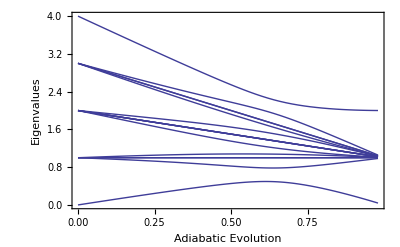

```mathematica
inihamilt=∑_(j=0)^3 1/2(Subscript[σ, 0,ĵ]-Subscript[σ, 𝒳,ĵ]);
hamilt[t_]:= (1-t)*inihamilt + t*myhamilt;
myeigenv[t_]:=Evaluate[Eigenvalues[QuantumMatrix[hamilt[t]]]];
Plot[myeigenv[t],{t,0,0.98},Frame->True,FrameLabel->{"Adiabatic Evolution","Eigenvalues"}]
```

Given that the system started at the lowest energy state of the initial Hamiltonian and that the evolution is adiabatic, the system will end in lowest energy state of the final Hamiltonian:

```mathematica
QuantumEigensystemForm[myhamilt,-1]
```

Eigenvalue | Eigenvector
0 | |1_OverHat[0],1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩

Then we can read (measure) the solution to the problem: |1_OverHat[0],1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ means that q0 must be TRUE, q1 must be TRUE, q2 must be FALSE and q3 must be TRUE, and that is the solution to our 3-SAT problem, which was previously stored in myexpr:

```mathematica
ReplaceAll[myexpr,{Subscript[q, 0]->True,Subscript[q, 1]->True,Subscript[q, 2]->False,Subscript[q, 3]->True}]
```

True

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx